```mathematica
<<OrbitalMotion`
```

```mathematica
<<RigidbodyKinematics`
```

## Trans & Rot, no RW, no Thrusters

```mathematica
a = 10000;
e = 0.01;
inc = 33.3 Degree;
AN = 48.2 Degree;
AP = -12.2 Degree;
f0 = 85.3 Degree;
```

```mathematica
μ = 0.3986004415 10^6
```

398600.

```mathematica
req = 0.6378136300 10^04
```

6378.14

```mathematica
{rVec0,vVec0} = elem2rv[μ,a,e,inc,AN,AP,f0]
```

(-4020.34 | 7490.57 | 5248.3
-5.19978 | -3.43668 | 1.04158)

```mathematica
{rVec0,vVec0}1000 (* convert to meters *)
```

(-4.02034×10^6 | 7.49057×10^6 | 5.2483×10^6
-5199.78 | -3436.68 | 1041.58)

```mathematica
M0 = E2M[f2E[f0,e],e]
```

1.46885

```mathematica
T = 10.*60
```

600.

```mathematica
ft = E2f[M2E[M0+Sqrt[μ/Abs[a]^3]T,e],e]
```

1.86683

```mathematica
{rVect,vVect}=elem2rv[μ,a,e,inc,AN,AP,ft]
```

(-6781.6 | 4946.87 | 5486.74
-3.89685 | -4.93817 | -0.253846)

```mathematica
{rVect,vVect}1000
```

(-6.7816×10^6 | 4.94687×10^6 | 5.48674×10^6
-3896.85 | -4938.17 | -253.846)

```mathematica
σBN = {0.1,0.2,-.3};
ωBN = {0.001,-0.01,0.03};
Inertia = DiagonalMatrix[{900.,800.,600}];
L = {0,0,0};
```

```mathematica
ans=NDSolve[{
σ'[t]==0.25 BmatMRP[σ[t]].ω[t],
Inertia.ω'[t]==-tilde[ω[t]].Inertia.ω[t]+L, 
σ[0]==σBN,
ω[0]==ωBN
},{σ,ω},{t,0,T}]
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

{{σ→InterpolatingFunction[{{0., 600.}}, <>],ω→InterpolatingFunction[{{0., 600.}}, <>]}}

```mathematica
MatrixForm[{σ[T],ω[T]}/.ans]
```

((-1.63193
-0.479066
3.08557) | (0.00708918
-0.00410849
0.0306095))

```mathematica
-σ[T]/(σ[T].σ[T]) /. ans
```

(0.131465 | 0.0385925 | -0.248567)

```mathematica
σ[T]/.ans
```

(-1.63193 | -0.479066 | 3.08557)

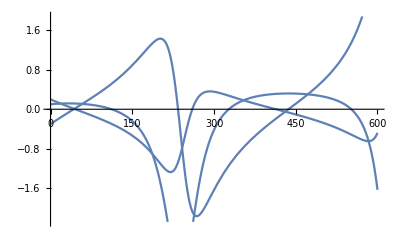

```mathematica
Plot[Evaluate[σ[t]/.ans[[1]]],{t,0,T}]
```

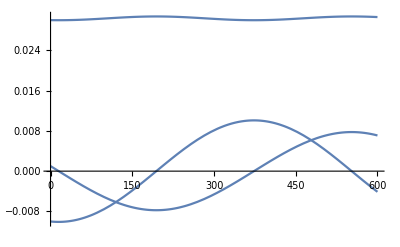

```mathematica
Plot[Evaluate[ω[t]/.ans[[1]]],{t,0,T}]
```

## Trans & Rot, 3-RWs, no Thrusters

```mathematica
a = 10000;
e = 0.01;
inc = 33.3 Degree;
AN = 48.2 Degree;
AP = -12.2 Degree;
f0 = 85.3 Degree;
```

```mathematica
μ = 0.3986004415 10^6
```

398600.

```mathematica
req = 0.6378136300 10^04
```

6378.14

```mathematica
{rVec0,vVec0} = elem2rv[μ,a,e,inc,AN,AP,f0]
```

(-4020.34 | 7490.57 | 5248.3
-5.19978 | -3.43668 | 1.04158)

```mathematica
{rVec0,vVec0}1000 (* convert to meters *)
```

(-4.02034×10^6 | 7.49057×10^6 | 5.2483×10^6
-5199.78 | -3436.68 | 1041.58)

```mathematica
M0 = E2M[f2E[f0,e],e]
```

1.46885

```mathematica
T = 10.*60
```

600.

```mathematica
ft = E2f[M2E[M0+Sqrt[μ/Abs[a]^3]T,e],e]
```

1.86683

```mathematica
{rVect,vVect}=elem2rv[μ,a,e,inc,AN,AP,ft]
```

(-6781.6 | 4946.87 | 5486.74
-3.89685 | -4.93817 | -0.253846)

```mathematica
{rVect,vVect}1000
```

(-6.7816×10^6 | 4.94687×10^6 | 5.48674×10^6
-3896.85 | -4938.17 | -253.846)

```mathematica
σBN = {0.1,0.2,-.3};
ωBN = {0.001,-0.01,0.03};
Ω0 = {0,0,0} RPM;
Inertia = DiagonalMatrix[{900.,800.,600}];
L = {0,0,0};
Js = 100/(6000. RPM);
Gs = Transpose[{
{1,0,0},
{0,1,0},
{0,0,1}
}];
us = {0.02,0.01,-0.05};
(*σBN = {0,0,0};
ωBN = {0,0,0};
Gs = Transpose[{
{1,0,0}
}];
us = {0.02};
Ω0 = {0} RPM;*)
```

```mathematica
ans=NDSolve[{
σ'[t]==0.25 BmatMRP[σ[t]].ω[t],
Inertia.ω'[t]==-tilde[ω[t]].(Inertia.ω[t]+Js Gs.(Transpose[Gs].ω[t]+Ω[t]))-Gs.us+L, 
Js (Ω'[t] + Transpose[Gs]. ω'[t])==us,
σ[0]==σBN,
ω[0]==ωBN,
Ω[0]== Ω0
},{σ,ω,Ω},{t,0,T}]
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

{{σ→InterpolatingFunction[{{0., 600.}}, <>],ω→InterpolatingFunction[{{0., 600.}}, <>],Ω→InterpolatingFunction[{{0., 600.}}, <>]}}

```mathematica
Table[{T i/5.,-σ[T i/5.]/Norm[σ[T i/5.]]^2}/.ans, {i,0,5}]
```

({0.,{-0.714286,-1.42857,2.14286}}
{120.,{0.220695,0.555722,-0.944517}}
{240.,{0.112872,-0.322785,0.684227}}
{360.,{0.258227,0.434358,-0.933064}}
{480.,{-1.41851,-1.62011,1.34615}}
{600.,{-0.0233055,-0.191127,0.493556}})

```mathematica
MatrixForm[Table[{T i/5.,Norm[σ[T i/5.]/.ans]},{i,0,5}]]
```

(0. | 0.374166
120. | 0.894554
240. | 1.30733
360. | 0.942409
480. | 0.393779
600. | 1.88757)

```mathematica
Table[{T i/5.,σ[T i/5.]}/.ans, {i,0,5}]
```

({0.,{0.1,0.2,-0.3}}
{120.,{-0.176606,-0.444704,0.755828}}
{240.,{-0.192911,0.551679,-1.16943}}
{360.,{-0.22934,-0.385768,0.828686}}
{480.,{0.219957,0.251217,-0.208736}}
{600.,{0.0830352,0.680968,-1.75849}})

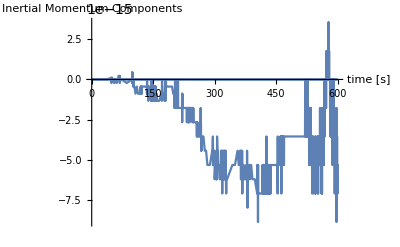

```mathematica
Plot[MRP2C[-σ[t]].(Inertia.ω[t]+Js Gs.(Transpose[Gs].ω[t]+Ω[t]))/.ans,{t,0,T},AxesLabel->{"time [s]","Inertial Momentum Components"}]
```

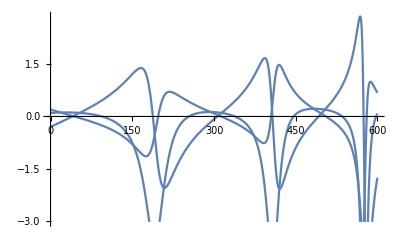

```mathematica
Plot[Evaluate[σ[t]/.ans[[1]]],{t,0,T}]
```

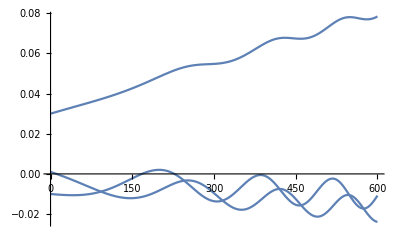

```mathematica
Plot[Evaluate[ω[t]/.ans[[1]]],{t,0,T}]
```

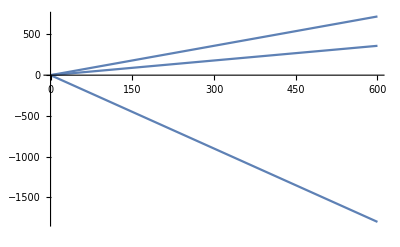

```mathematica
Plot[Evaluate[Ω[t]/.ans[[1]]]/RPM,{t,0,T}]
```